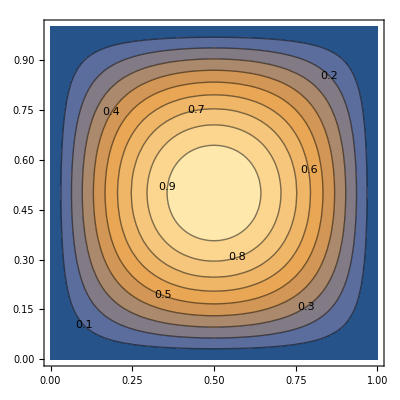

```mathematica
ContourPlot[Sin[π x]Sin[π y],{x,0,1},{y,0,1},ContourLabels->True]
```

D=1

```mathematica
Yt0={{0.12820327,0.22193484,0.25643804,0.22251404,0.12892714},
{0.22094124,0.38258492,0.44208114,0.38352318,0.22211369},
{0.2542195,0.44031347,0.50881688,0.44137268,0.2555429},{0.21958957,0.38041665,0.43963917,0.38135314,0.22075949},{0.12652609,0.21924443,0.25340801,0.21982143,0.12724682}};
```

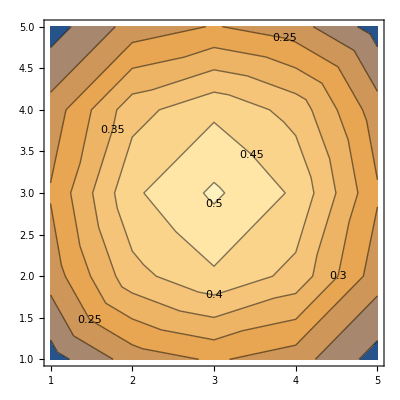

```mathematica
ListContourPlot[Yt0,ContourLabels->True]
```

```mathematica
Yt1={{0.13176842,0.22791005,0.26345447,0.22900328,0.13313506},
{0.22601051,0.39113604,0.4521805,0.39291239,0.22823079},{0.2592049,0.44878993,0.51889849,0.45080421,0.26172218},{0.22338754,0.38693856,0.44746374,0.38872946,0.22562531},{0.12851109,0.222697,0.257596,0.22380746,0.12989842}};
```

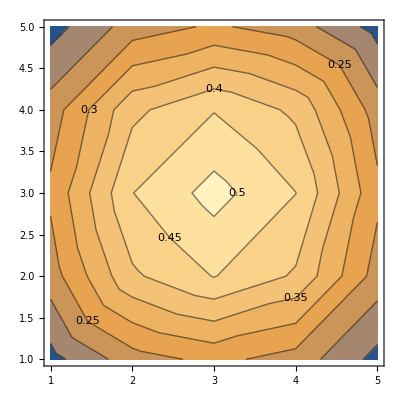

```mathematica
ListContourPlot[Yt1,ContourLabels->True]
```

```mathematica
Yt2={{0.1356661,0.2343834,0.27099342,0.2359238,0.13759223},
{0.23167477,0.40058688,0.46323308,0.40309672,0.23481262},
{0.26492224,0.45838292,0.53017392,0.46124118,0.26849508},
{0.22788051,0.39452923,0.45644062,0.39708475,0.23107434},
{0.13094953,0.22685202,0.26254714,0.22844693,0.13294245}};
```

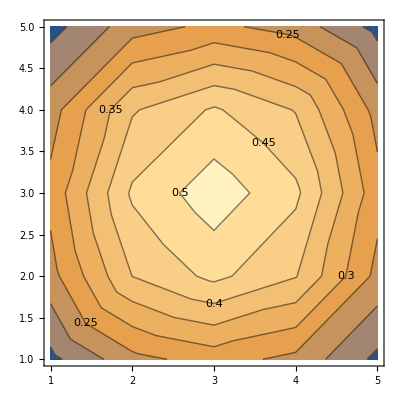

```mathematica
ListContourPlot[Yt2,ContourLabels->True]
```

```mathematica
Yt3={{0.13986558,0.24130531,0.27899916,0.24322644,0.14226832},
{0.23788994,0.41086539,0.4751569,0.41400314,0.24181371},
{0.27132977,0.46902282,0.54256257,0.47261069,0.27581562},
{0.23304011,0.40313983,0.4665118,0.4063653,0.23707206},
{0.13382995,0.23168856,0.26823538,0.23371481,0.13636233}};
```

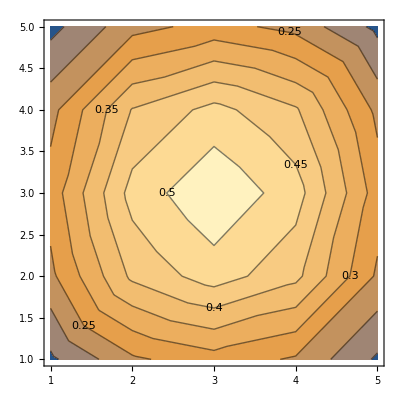

```mathematica
ListContourPlot[Yt3,ContourLabels->True]
```

```mathematica
Yt4={{0.14433582,0.24862678,0.28741763,0.25086433,0.14713492},
{0.24460906,0.42189662,0.4878685,0.42555865,0.24918944},
{0.27837983,0.48063243,0.55597729,0.4848356,0.28363609},
{0.23883066,0.41271134,0.4776094,0.41651002,0.24358012},
{0.13713544,0.23717771,0.27462653,0.23957959,0.14013784}};
```

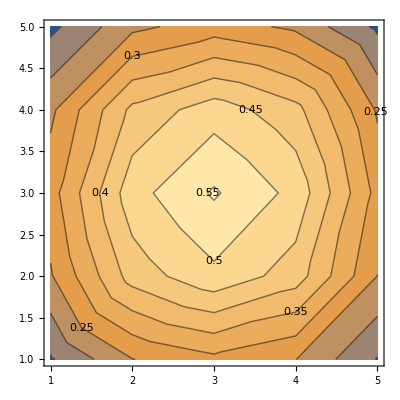

```mathematica
ListContourPlot[Yt4,ContourLabels->True]
```

It gets higher - it should decrease. What’s going on?

D=0.1

```mathematica
Yt0={{0.12475066,0.21715302,0.25192338,0.21928557,0.12740194},
{0.21262895,0.37015651,0.42916403,0.3730617,0.21625666},
{0.24276684,0.42259972,0.48965679,0.42509974,0.24589543},
{0.20835934,0.3627419,0.42013995,0.36441467,0.21045396},
{0.11920878,0.20761214,0.24043115,0.20840796,0.1202059}};
```

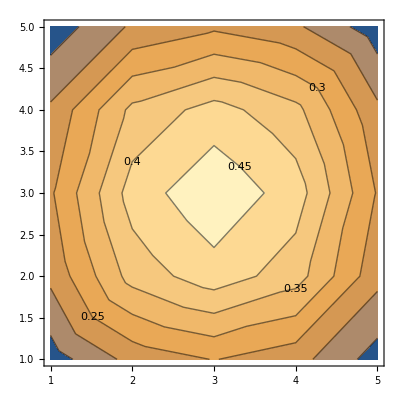

```mathematica
ListContourPlot[Yt0,ContourLabels->True]
```

D=0.01

```mathematica
Yt0={{0.12564684,0.2179651,0.25210826,0.21878448,0.12666787},
{0.21643915,0.37553832,0.43434234,0.37682066,0.21803851},
{0.24883132,0.43180876,0.49939717,0.43314688,0.25050329},
{0.21464192,0.37255506,0.43086773,0.37363303,0.21599082},
{0.12339944,0.21425565,0.24781421,0.21486969,0.1241682}};
```

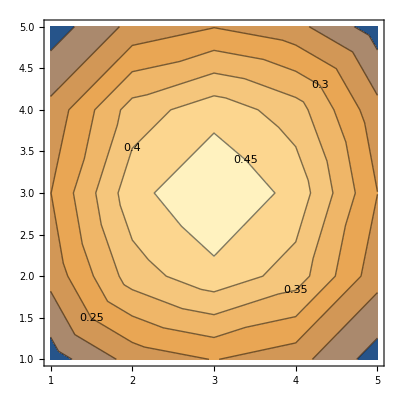

```mathematica
ListContourPlot[Yt0,ContourLabels->True]
```

D=1e-6

```mathematica
Yt0={{0.12567828,0.21797505,0.25207456,0.21871553,0.12660125},{0.21661284,0.37575222,0.43450999,0.37690451,0.21805041},{0.2491576,0.43226225,0.49982821,0.4334582,0.25065229},{0.21503989,0.37313416,0.43145252,0.37409203,0.21623882},{0.12371128,0.21472013,0.24829687,0.2152624,0.12439044}};
```

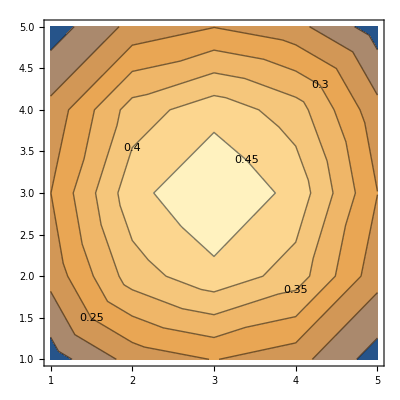

```mathematica
ListContourPlot[Yt0,ContourLabels->True]
```

Analytical solution for 1-D

```mathematica
pde=D[ψ[x,t], t]-𝒟 D[ψ[x,t], x,x]==0;
```

```mathematica
bct0=ψ[x,0]==Sin[π x];
```

```mathematica
bcx0=ψ[0,t]==0;
```

```mathematica
bcx1=ψ[1,t]==0;
```

```mathematica
sol=DSolve[{pde,bct0},ψ[x,t],{x,t}]
```

{{ψ[x,t]→ⅇ^(-π^2 t 𝒟) Sin[π x]}}

```mathematica
NDSolve[{pde,ic},ψ[x,t],{x,0,1},{t,0,1}]
```

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve[{ψ^(0,1)[x,t]-𝒟 ψ^(2,0)[x,t]==0,ψ[x,0]==Sin[π x]},ψ[x,t],{x,0,1},{t,0,1}]

Analytical solution for 2-D

```mathematica
pde=D[ψ[x,y,t], t]-𝒟(D[ψ[x,y,t], x,x]+D[ψ[x,y,t], y,y])==0
```

ψ^(0,0,1)[x,y,t]-𝒟 (ψ^(0,2,0)[x,y,t]+ψ^(2,0,0)[x,y,t])==0

```mathematica
bcx0=ψ[0,y,t]==0
```

ψ[0,y,t]==0

```mathematica
bcx1=ψ[1,y,t]==0
```

ψ[1,y,t]==0

```mathematica
bcy0=ψ[x,0,t]==0
```

ψ[x,0,t]==0

```mathematica
bcy1=ψ[x,1,t]==0
```

ψ[x,1,t]==0

```mathematica
bct0=ψ[x,y,0]==Sin[π x]Sin[π y]
```

ψ[x,y,0]==Sin[π x] Sin[π y]

```mathematica
DSolve[{pde,bct0},ψ[x,y,t],{x,0,1},{y,0,1},{t,0,1}]
```

DSolve[{ψ^(0,0,1)[x,y,t]-𝒟 (ψ^(0,2,0)[x,y,t]+ψ^(2,0,0)[x,y,t])==0,ψ[x,y,0]==Sin[π x] Sin[π y]},ψ[x,y,t],{x,0,1},{y,0,1},{t,0,1}]